```mathematica
Msun=1476.7;
r0=10^5;
c=1;
μe=2;
me=6.7648*10^-58;
mH=1.2428*10^-54;
h=1.6414*10^-69;
cSI=2.9979*10^8;
GSI=6.6741*10^-11;
ϵ0SI=8.8542*10^-12;
convFact=cSI^2*Sqrt[ϵ0SI/GSI];
e=1.6022*10^-19/convFact;
(*4*π*ϵ0==1*)
```

```mathematica
p[ρ[x_]]:=(Pi*me^4*c^5)/(3*h^3)*((((3*h^3*ρ[x])/(8*Pi*μe*mH*(me*c)^3))^(1/3))*(2*(((3*h^3*ρ[x])/(8*Pi*μe*mH*(me*c)^3))^(1/3))^2-3)*Sqrt[(((3*h^3*ρ[x])/(8*Pi*μe*mH*(me*c)^3))^(1/3))^2+1]+3*ArcSinh[((3*h^3*ρ[x])/(8*Pi*μe*mH*(me*c)^3))^(1/3)]);
ρq[ρ[x_]]:=α*e/mH*ρ[x];
```

```mathematica
sol=NDSolve[{D[q[x],x]/r0==4*Pi*ρq[ρ[x]]*(r0*x)^2*(1-(2*Msun*y[x])/(r0*x)+q[x]^2/(r0*x)^2)^(-1/2),D[p[ρ[x]],x]/r0==-(p[ρ[x]]+ρ[x])/((r0*x)*(r0*x-2*Msun*y[x]+q[x]^2/(r0*x)))*(4*Pi*p[ρ[x]]*(r0*x)^3+Msun*y[x]-q[x]^2/(r0*x))+(q[x]*D[q[x],x]/r0)/(4*Pi*(r0*x)^4),(Msun*D[y[x],x])/r0==4*Pi*(r0*x)^2*ρ[x]+(q[x]*D[q[x],x]/r0)/(r0*x),q[10^-5]==10^-10,y[10^-5]==10^-10,ρ[10^-5]==ρc}/.{α->0(*5*10^-19*),ρc->1.9*10^13*7.4262*10^-28},{q,ρ,y},{x,10^-5,12}]
```

{{q→InterpolatingFunction[…],ρ→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

10.8241

1.40209

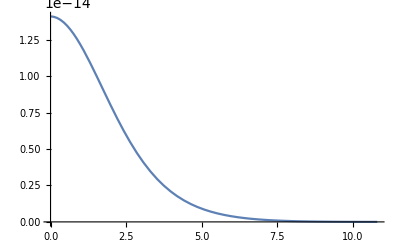
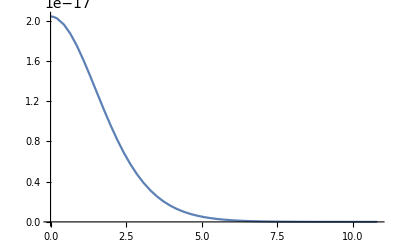
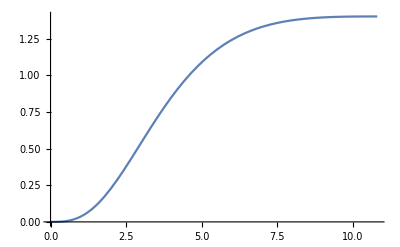
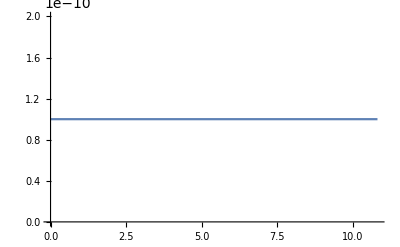

```mathematica
radius=x/.FindRoot[p[ρ[x]]/.sol,{x,1}]//Re//Quiet
mass=y[radius]/.sol[[1]]//Re
{Plot[ρ[x]/.sol,{x,10^-5,radius}],Plot[p[ρ[x]]/.sol,{x,10^-5,radius}],Plot[y[x]/.sol,{x,10^-5,radius}],Plot[q[x]/.sol,{x,10^-5,radius}]}
```

```mathematica
sol=NDSolve[{D[q[x],x]/r0==4*Pi*ρq[ρ[x]]*(r0*x)^2*(1-(2*Msun*y[x])/(r0*x)+q[x]^2/(r0*x)^2)^(-1/2),D[p[ρ[x]],x]/r0==-(p[ρ[x]]+ρ[x])/((r0*x)*(r0*x-2*Msun*y[x]+q[x]^2/(r0*x)))*(4*Pi*p[ρ[x]]*(r0*x)^3+Msun*y[x]-q[x]^2/(r0*x))+(q[x]*D[q[x],x]/r0)/(4*Pi*(r0*x)^4),(Msun*D[y[x],x])/r0==4*Pi*(r0*x)^2*ρ[x]+(q[x]*D[q[x],x]/r0)/(r0*x),q[10^-5]==10^-10,y[10^-5]==10^-10,ρ[10^-5]==ρc}/.{α->5*10^-20,ρc->1.9*10^13*7.4262*10^-28},{q,ρ,y},{x,10^-5,12}]
```

{{q→InterpolatingFunction[…],ρ→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

11.061

1.48726

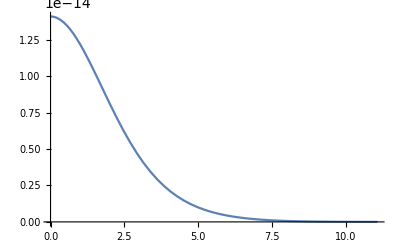
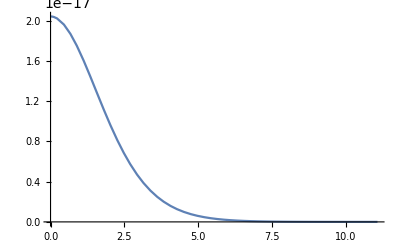
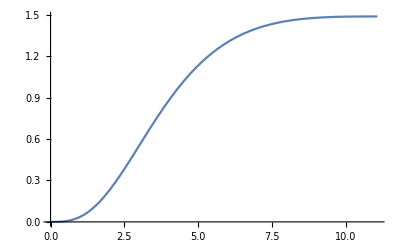
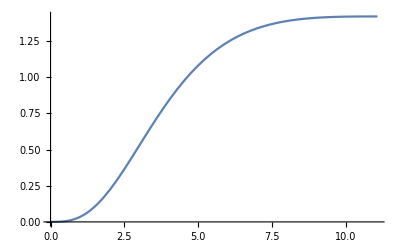

```mathematica
radius=x/.FindRoot[p[ρ[x]]/.sol,{x,1}]//Re//Quiet
mass=y[radius]/.sol[[1]]//Re
{Plot[ρ[x]/.sol,{x,10^-5,radius}],Plot[p[ρ[x]]/.sol,{x,10^-5,radius}],Plot[y[x]/.sol,{x,10^-5,radius}],Plot[(convFact*q[x])/10^19/.sol,{x,10^-5,radius}]}
```